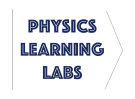
# -Graphics- Lab 4 - Energy Conservation

In this lab we will release a Smart Cart from rest on an inclined ramp. As it reaches the bottom, it will undergo a collision and be repelled back up the ramp where the process is again repeated. We will track the conservation of mechanical energy after each bounce given i) magnetic repulsion and ii) elastic rubber repulsion.

## Background

Based on the Fig.(1), we will be releasing the cart from rest, allowing it to accelerate along the ramp.

As you have determined in Prelab 4, the cart will have kinetic energy

KE = 1/2 mv^2.

The gravitational potential energy will be given as

GE = -mg x(t) sin(θ) .

The mechanical energy E is therefore

E = KE + GE 
     = 1/2 mv^2- mg x(t) sin(θ)

** In the Capstone measurement software, the initial height of the cart before release corresponds to x(0)=0. Hence as the cart travels down the ramp, its position x(t) will increase.

## Experiment

### Calibration and Capstone Introduction

Download the .nb and .cap file. Open the .cap file with Pasco Capstone and turn on your Smart Cart.

Connect the Smart Cart via Bluetooth by entering  and double-clicking on the cart with matching serial numbers

#### Angle Calibration

We will use the accelerometers to determine the angle of the ramp. Once this angle is determined, it will be implemented inside Capstone calculations to eventually plot the gravitational potential and mechanical energy.

Place the cart near the bottom of the ramp with the two magnetic bumpers facing each other (i.e. repelling each other)

Make sure the system is at rest and no longer oscillating. Click on the  tab and click  .  Once you have ~ 10 sec worth of data, stop recording.

Find the mean of the angle data from the graph using the tools  and .

Within the  section, replace the value of θ with the angle you determined above

Delete the calibration data by selecting

#### Mass Calibration

Using the weigh scale, measure the mass of the Smart Cart with the attached rubber elastic bumper.

Enter this mass as m (elast) within the Capstone calculations section.

Remove the small elastic bumper and attach the small magnetic bumper. Weigh the cart with magnetic bumper and record this mass under m (mag) within the calculations section.

The mass values are to be given in kg units.

### Data Collection

Now that we have calibrated the mass and angle of our system, we will use Capstone to directly plot the gravitational potential energy, kinetic energy, and mechanical energy. These energy calculations have already been coded into the Lab_4.cap experiment. Only one quality trial for each repulsion type is needed.

#### Magnetic Repulsion

Go to the  tab

Student 1 is to move the cart such that the front edge of the cart magnetic bumper is located ~20-30 cm from the magnetic bumper at the bottom of the track (Fig. (2)). Do not exceed this distance or you may damage the equipment.

Student 2 will click  and once Capstone begins measuring and displays zero PE, Student 1 may then release the cart. The sequence of recording then releasing is important, or else the initial potential energy will not register appropriately. It also important that no initial velocity is imparted upon the cart upon release.

Record 10-15 seconds worth of data, then stop the recording.

You may auto-scale the data in each plot by selecting

Your data should resemble something similar to the image below

#### Elastic Repulsion

Unfasten the magnetic bumper and attach the elastic rubber bumper

Go to the  tab

Repeat the same procedure as in Magnetic Repulsion. You will only need ~ 4-5 seconds worth of data in the elastic case

If you would like view to specific runs, use the tool

Your data should resemble something similar to the image below

### Computation

Our objective here will be to plot the mechanical energy as a function of n, the bounce number.

To achieve this, we note that for each bounce there is a region where the mechanical energy is approximately constant. In such a region, we may use the select and mean tools  -Graphics- -Graphics- to find the average energy, which will then be stored into a Mathematica list. An example of such a region is indicated below.

Compose an ordered list magnetic of ~ 10 elements that represent the mechanical energy after each bounce for the magnetic bumpers. The first element should be approximately zero energy and the list should be of the form {E_1, E_2, E_3,..., E_n}

```mathematica
magnetic =
```

Compose an ordered list elastic of ~ 5 elements that represent the mechanical energy after each bounce for the elastic bumper. The first element should be approximately zero energy and the list should be of the form {E_1, E_2, E_3,..., E_n}

```mathematica
elastic=
```

Use ListPlot to plot the mechanical energy vs. bounce number for each case above. Store as variables magneticplot and elasticplot . (Note that since our x axis is just the discrete index n, the lists created above are already in the proper plot format).

```mathematica
magneticplot=ListPlot[magnetic]
```

```mathematica
elasticplot= ListPlot[elastic,PlotStyle->Red]
```

Instead of using Show, use ListPlot[{list1,list2}] to superimpose the two discrete plots into a single graph labeled finalplot. Label the axes appropriately and use the option PlotLegends→{“1”,”2”} to add an appropriate legend.

```mathematica
finalplot=ListPlot[{magnetic,elastic},PlotRange->All,PlotLegends->{"Magnetic","Elastic"},AxesLabel->{"n","E (J)"}]
```

## Analysis

Why is the mechanical energy negative? Does this violate the definition of mechanical energy?

Take a screenshot of the Capstone graph of E mag(t) and paste below.

What happens to the mechanical energy during the collision with the magnetic bumpers? Where does it go?

Take a screenshot of the Capstone graph of E elast(t) and paste below.

What happens to the mechanical energy during the collision with the elastic bumper? Where does it go?

Paste an image of the magnetic/elastic mechanical energy vs. n below.

Why is the mechanical energy not conserved over time?  Does this necessarily mean the magnetic or elastic forces must be non-conservative?

Based on your plot, describe the decrease in mechanical energy over time for each repulsion (i.e. describe the functional form/shape of the plot)

Which set of bumpers was more efficient at conserving the mechanical energy? Why do you think this is the case?

Do you expect mechanical energy to always be conserved in realistic physical scenarios? Why or why not?

Provide a detailed summary of this lab. What was our objective? What did our data indicate about the conservation of mechanical energy? What other forms of work and energy should be included with mechanical energy to provide a reasonable model for our system?

# Submit this completed notebook as a .pdf into HuskyCT. (Make sure all cells sections are visible to receive credit for all your output. As a shortcut, use CTRL+A then CTRL+SHIFT+[ to open all cell sections).